```mathematica
(*Created 2017 by CunhaJ 
The aim of this notebook is to implement a transfer matrix formalism and compute electronic transmission across discontinuities of potentials *)
```

1/1000000000

10.

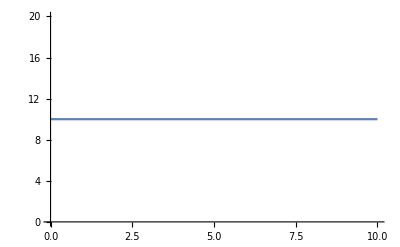

InterpolatingFunction[{{0., 13.}}, <>]

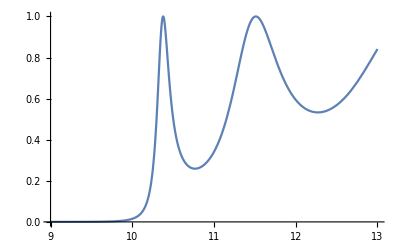

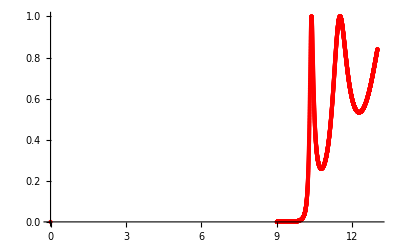

-Graphics-

```mathematica
(*Consistency*check*) 

(*mass of the electron in kg*)
m=9.1*10^(-31);
(*value of Planck constant in eV.s*)
hbar=6.6*10^(-16);
(*workfunction of metal 1 in eV*)
phi1=10;
(*workfunction of metal2 in eV*)
phi2=10;
(*charge of the electron in C*)
qe=1.6*10^(-19);
(*max incoming electron energy in eV*)
EN=13;
(*applied bias in V*)
VD=0;
(*Total number of division of tunnel barrier*)
Ntot=10;
(*thickness of the oxide layer in m*)
dox=1*10^(-9);
(*alpha goes from 1 to Ntot !!!!!! *)
dx=dox/Ntot;
(********************BEGGINING OF CALCULATION OF TRANSMISSION COEFFICIENT***)

deltaz[alpha_]:=alpha*dx
deltaz[Ntot]


Pot[alpha_,VD_]:=phi1-(phi1-(phi2+VD))*alpha/Ntot
Potx[x_,VD_]:=phi1-(phi1-(phi2+VD))*x/dox
Pot[Ntot,VD]//N

k2[alpha_,energy_]:=Sqrt[(2*m/(hbar*1.6*10^(-19))^2)*(energy-Pot[alpha,VD])*1.6*10^(-19)]
k1[energy_]:=Sqrt[(2*m/(hbar*1.6*10^(-19))^2)*(energy)*1.6*10^(-19)]

(*Potentialo barrier as function of the parameter Alpha (the number of sub-barrier) in the potential*)
Plot[Pot[alpha,VD],{alpha,0,Ntot}, PlotRange->Automatic]

T31[alpha_,energy_]:={{Exp[-I*k1[energy]*dox],0},{0,Exp[I*k1[energy]*dox]}}.{{(k2[alpha,energy]+k1[energy])/(2*k2[alpha,energy]),(-k2[alpha,energy]+k1[energy])/(2*k2[1,energy])},{(-k2[alpha,energy]+k1[energy])/(2*k2[alpha,energy]),(k2[alpha,energy]+k1[energy])/(2*k2[alpha,energy])}}.{{Exp[I*k2[alpha,energy]*dox],0},{0,Exp[-I*k2[alpha,energy]*dox]}}.{{(k2[alpha,energy]+k1[energy])/(2*k1[energy]),(k2[alpha,energy]-k1[energy])/(2*k1[energy])},{(k2[alpha,energy]-k1[energy])/(2*k1[energy]),(k2[alpha,energy]+k1[energy])/(2*k1[energy])}}
(*T31[ALP,ENERG]//FullSimplify//TraditionalForm*)
coeffs={{0,0}};
j=0;
For[en=9,en<EN,en=en+0.001,j++;AppendTo[coeffs,{en,1/Abs[T31[Ntot,en][[2,2]]]^2}]]

f=Interpolation[coeffs]
Trans[en_]:=(1+(phi1)^2*Sinh[Sqrt[2*m*(phi1-en)*1.6*10^(-19)/(hbar*(1.6*10^(-19)))^2]*dox]^2/(4*en*(phi1-en)))^(-1)

plot1=Plot[Trans[en],{en,09,EN},PlotRange->Automatic]

plot2=ListPlot[coeffs, PlotStyle->{PointSize@Small,Red}]
Show[plot1,plot2, Plot[f[en],{en,0,EN}, PlotStyle->{LineColor->Green}], Frame-> True,FrameLabel-> {"E (eV)","Transmission"}, GridLines-> Automatic, GridLinesStyle->Directive[Dotted, Gray]]
```

```mathematica
(***************************
Now, stepped barrier
********)
```

```mathematica
Clear["Global`*"]
```

```mathematica
(*mass of the electron in kg*)
m=9.1*10^(-31);
(*value of Planck constant in eV.s*)
hbar=6.6*10^(-16);
(*workfunction of metal 1 in eV*)
phi1=10;
(*workfunction of metal2 in eV*)
phi2=11;
(*charge of the electron in C*)
qe=1.6*10^(-19);
(*max incoming electron energy in eV*)
EN=12;
(*applied bias in V*)
VD=0;
(*Total number of division of tunnel barrier*)
Ntot=1;
(*thickness of the oxide layer in m*)
dox=3*10^(-9);
(*alpha goes from 1 to Ntot !!!!!! *)
dx=dox/Ntot;
(********************BEGGINING OF CALCULATION OF TRANSMISSION COEFFICIENT***)
```

```mathematica
(*Simple check for matrix multiplication*)
T[K1_,K2_,doxide_]:={{Exp[-I*K1*doxide/2],0},{0,Exp[I*K1*doxide/2]}}.{{(K1+K2)/(2*K2),(K1-K2)/(2*K2)},{(K1-K2)/(2*K2),(K1+K2)/(2*K2)}}.{{Exp[I*K2*doxide/2],0},{0,Exp[-I*K2*doxide/2]}}.
{{Exp[I*K2*doxide/2],0},{0,Exp[-I*K2*doxide/2]}}.{{(K1+K2)/(2*K1),(K2-K1)/(2*K1)},{(K2-K1)/(2*K1),(K1+K2)/(2*K1)}}.{{Exp[-I*K1*doxide/2],0},{0,Exp[I*K1*doxide/2]}}
```

```mathematica
T[K1,K2,doxide]//MatrixForm
```

(ⅇ^(-1/2 ⅈ doxide K1) ((ⅇ^(-1/2 ⅈ doxide K1-ⅈ doxide K2) (K1-K2) (-K1+K2))/(4 K1 K2)+(ⅇ^(-1/2 ⅈ doxide K1+ⅈ doxide K2) (K1+K2)^2)/(4 K1 K2)) | ⅇ^((ⅈ doxide K1)/2) ((ⅇ^(-1/2 ⅈ doxide K1-ⅈ doxide K2) (K1-K2) (K1+K2))/(4 K1 K2)+(ⅇ^(-1/2 ⅈ doxide K1+ⅈ doxide K2) (-K1+K2) (K1+K2))/(4 K1 K2))
ⅇ^(-1/2 ⅈ doxide K1) ((ⅇ^((ⅈ doxide K1)/2+ⅈ doxide K2) (K1-K2) (K1+K2))/(4 K1 K2)+(ⅇ^((ⅈ doxide K1)/2-ⅈ doxide K2) (-K1+K2) (K1+K2))/(4 K1 K2)) | ⅇ^((ⅈ doxide K1)/2) ((ⅇ^((ⅈ doxide K1)/2+ⅈ doxide K2) (K1-K2) (-K1+K2))/(4 K1 K2)+(ⅇ^((ⅈ doxide K1)/2-ⅈ doxide K2) (K1+K2)^2)/(4 K1 K2)))

```mathematica
(*Expression for the transmitted wave amplitude - in accordance with the Optoelectronics Notes*)
ExpToTrig[T[K1,K2,doxide][[2,2]]]//FullSimplify
```

-(ⅈ ⅇ^(ⅈ doxide K1) (2 ⅈ K1 K2 Cos[doxide K2]+(K1^2+K2^2) Sin[doxide K2]))/(2 K1 K2)

```mathematica
-1/(2 K1 K2)ⅈ ⅇ^(ⅈ doxide K1) (2 4ⅈ K1 K2 Cos[doxide K2]+(K1^2+K2^2) Sin[doxide K2])
```

-(ⅈ ⅇ^(ⅈ doxide K1) (8 ⅈ K1 K2 Cos[doxide K2]+(K1^2+K2^2) Sin[doxide K2]))/(2 K1 K2)

```mathematica
(*Expression for the reflected wave amplitude*)
ExpToTrig[T[K1,K2,doxide][[1,2]]]//FullSimplify
```

-(ⅈ (K1-K2) (K1+K2) Sin[doxide K2])/(2 K1 K2)

```mathematica
Potx[x_,VD_]:=If[x<0||x>dox,0,phi1-(phi1-(phi2+VD))*x/dox]
```

```mathematica
kvecx[x_,energy_]:=Sqrt[(2*m/(hbar*1.6*10^(-19))^2)*(energy-Potx[x,VD])*1.6*10^(-19)]
```

```mathematica
Abs[T[kvecx[-dox,8],kvecx[dox/2,8],dox][[2,2]]]^2
```

3.90266×10^20

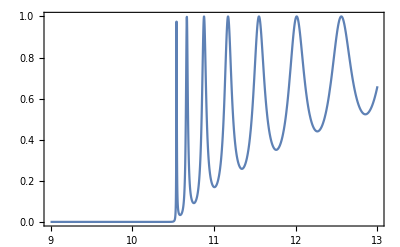

```mathematica
Plot[1/Abs[T[kvecx[-dox,energy],kvecx[dox/2,energy],dox][[2,2]]]^2,{energy,9,13},Frame->True]
```

```mathematica
(*************************************************************All The matrix calculations*)
Clear["Global`*"]
SetOptions[Plot,BaseStyle->FontSize->15]
(*mass of the electron in kg*)
m=9.1*10^(-31);
(*value of Planck constant in eV.s*)
hbar=6.6*10^(-16);

(*!!! CALCULATIONS COMPUTED FOR Cr/Cr2O3/Pd system (such as in Eliasson PhD thesis)*)
(*workfunction of metal 1 in eV - for Cr*)
phi1=10.74;
(*workfunction of metal2 in eV for Pd*)
phi2=12.36;
(*Fermi Energy*)
EFermi=10;
(*charge of the electron in C*)
qe=1.6*10^(-19);
(*max incoming electron energy in eV*)
EN=13;
(*applied bias in V*)
VD=0;
(*Total number of division of tunnel barrier*)
Ntot=100;
(*thickness of the oxide layer in m*)
dox=3*10^(-9);
(*alpha goes from 1 to Ntot !!!!!! *)
dx=dox/Ntot;
(********************BEGGINING OF CALCULATION OF TRANSMISSION COEFFICIENT***)
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→FontSize→15,ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

```mathematica
SetOptions[$FrontEndSession,EvaluationCompletionAction->"ShowTiming"]
```

```mathematica
(*Bandstructure parameters, EFermi, taken arbitrarily as 10 eV, all units in eV*)
EFermi=10;
phif1=4.5;
phif2=4.5;
electaff=3.76;

(*Definition of potential barrier potential*)
Potx[x_,VD_]:=If[x<0||x>dox,
If[x>dox,VD,0],
(EFermi+(phif1-electaff))-((EFermi+(phif1-electaff))-((EFermi+(phif2-electaff))+VD))*x/dox]
```

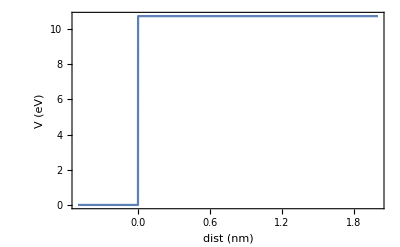

```mathematica
(*In the case that VD is zero, this should comprise the fact that the Fermi levels are aligned and therefore the upper barrier is tilted*)
Plot[Potx[x*10^(-9),VD],{x,-1/2,2}, Frame->True, FrameLabel->{"dist (nm)","V (eV)"}]
```

```mathematica
(*momentum vector*)
kvecx[x_,energy_]:=Sqrt[(2*m/(hbar*1.6*10^(-19))^2)*(energy-Potx[x,VD])*1.6*10^(-19)]
```

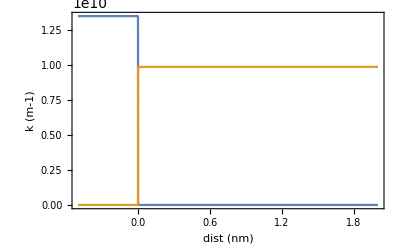

```mathematica
(*plot of real and imaginary part of momentum vector*)
Plot[{Re[kvecx[x*10^(-9),7]], Im[kvecx[x*10^(-9),7]]},{x,-1/2,2}, Frame->True, FrameLabel->{"dist (nm)","k (m-1)"}]
```

```mathematica
(*Staircase interpolation of the potential barrier - FROM 0-energy*)

interpx[x0_,VD0_]:=Module[{x=x0,VD=VD0},
data=Table[{alpha,((EFermi+(phif1-electaff))-((EFermi+(phif1-electaff))-((EFermi+(phif2-electaff))+VD))*alpha/Ntot)},{alpha,0,Ntot}];
If[x<0||x>dox,return=If[x>dox,VD,0],return=ListInterpolation[data[[All,2]],{{0,Ntot}},InterpolationOrder->0][x/dx]];
return]
```

```mathematica
Ntot=100
```

100

```mathematica
Plot[{Potx[x*10^(-9),VD],interpx[x*10^(-9),VD]},{x,-1/2,5}, Frame->True, FrameLabel->{"dist (nm)","V (eV)"},Epilog->Style[Text[StringJoin["VD=",ToString[VD]," V"],{Center, Center}],14]]
```

-Graphics-

```mathematica
(*Same but with barrier from Fermi energy instead*)
interpFermi[x0_,VD0_]:=Module[{x=x0,VD=VD0},
data=Table[{alpha,((EFermi+(phif1-electaff))-((EFermi+(phif1-electaff))-((EFermi+(phif2-electaff))+VD))*alpha/Ntot)},{alpha,0,Ntot}];
If[x<0||x>dox,return=If[x>dox,VD+EFermi,EFermi],return=ListInterpolation[data[[All,2]],{{0,Ntot}},InterpolationOrder->0][x/dx]];
return]
```

```mathematica
Ntot=600
```

600

```mathematica
Plot[{Potx[x*10^(-9),VD],interpFermi[x*10^(-9),VD]},{x,-1/2,5}, Frame->True, FrameLabel->{"dist (nm)","V (eV)"},Epilog->Style[Text[StringJoin["VD=",ToString[VD]," V"],{Center, Center}],14]]
```

-Graphics-

```mathematica
Clear[kvecx] (*clear kvecx*)
```

```mathematica
Tstep[x_,energy_]:=
{{Exp[-I*kvecx[x,energy]*x],0},{0,Exp[I*kvecx[x,energy]*x]}}.{{(kvecx[x,energy]+kvecx[x-dx,energy])/(2*kvecx[x-dx,energy]),(kvecx[x,energy]-kvecx[x-dx,energy])/(2*kvecx[x-dx,energy])},{(kvecx[x,energy]-kvecx[x-dx,energy])/(2*kvecx[x-dx,energy]),(kvecx[x,energy]+kvecx[x-dx,energy])/(2*kvecx[x-dx,energy])}}.{{Exp[I*kvecx[x-dx,energy]*x],0},{0,Exp[-I*kvecx[x-dx,energy]*x]}}
```

```mathematica
(*For debug, value of Tstep matrix in the beggining*)
Tstep[0,en]//TableForm
```

(kvecx[-3/100000000000,en]+kvecx[0,en])/(2 kvecx[-3/100000000000,en]) | (-kvecx[-3/100000000000,en]+kvecx[0,en])/(2 kvecx[-3/100000000000,en])
(-kvecx[-3/100000000000,en]+kvecx[0,en])/(2 kvecx[-3/100000000000,en]) | (kvecx[-3/100000000000,en]+kvecx[0,en])/(2 kvecx[-3/100000000000,en])

```mathematica
Tstep[dox,en]//TableForm
```

(ⅇ^((3 ⅈ kvecx[297/100000000000,en])/1000000000-(3 ⅈ kvecx[3/1000000000,en])/1000000000) (kvecx[297/100000000000,en]+kvecx[3/1000000000,en]))/(2 kvecx[297/100000000000,en]) | (ⅇ^(-(3 ⅈ kvecx[297/100000000000,en])/1000000000-(3 ⅈ kvecx[3/1000000000,en])/1000000000) (-kvecx[297/100000000000,en]+kvecx[3/1000000000,en]))/(2 kvecx[297/100000000000,en])
(ⅇ^((3 ⅈ kvecx[297/100000000000,en])/1000000000+(3 ⅈ kvecx[3/1000000000,en])/1000000000) (-kvecx[297/100000000000,en]+kvecx[3/1000000000,en]))/(2 kvecx[297/100000000000,en]) | (ⅇ^(-(3 ⅈ kvecx[297/100000000000,en])/1000000000+(3 ⅈ kvecx[3/1000000000,en])/1000000000) (kvecx[297/100000000000,en]+kvecx[3/1000000000,en]))/(2 kvecx[297/100000000000,en])

```mathematica
T=Tstep[dox,en].Tstep[0,en];
```

```mathematica
(*Seems to give comparable results to the ones computed with the simple method*)
ExpToTrig[T[[2,2]]]//FullSimplify
```

(ⅇ^((3 ⅈ kvecx[3/1000000000,en])/1000000000) (Cos[(3 kvecx[297/100000000000,en])/1000000000] (kvecx[-3/100000000000,en] kvecx[297/100000000000,en]+kvecx[0,en] kvecx[3/1000000000,en])-ⅈ (kvecx[0,en] kvecx[297/100000000000,en]+kvecx[-3/100000000000,en] kvecx[3/1000000000,en]) Sin[(3 kvecx[297/100000000000,en])/1000000000]))/(2 kvecx[-3/100000000000,en] kvecx[297/100000000000,en])

```mathematica
(*Transmission analytical coefficient for the square barrier*)
Trans[en_]:=(1+(phi1)^2*Sinh[Sqrt[2*m*(phi1-en)*1.6*10^(-19)/(hbar*(1.6*10^(-19)))^2]*dox]^2/(4*en*(phi1-en)))^(-1)
```

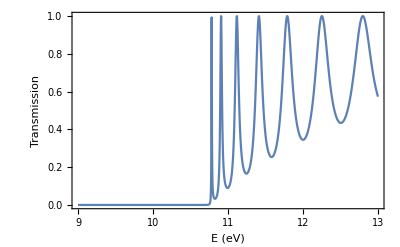

```mathematica
plot1=Plot[Trans[en],{en,09,EN},PlotRange->Automatic, Frame->True, FrameLabel->{{"Transmission",},{"E (eV)","Analytical transmission coefficient"}}]
```

```mathematica
VD
```

0

```mathematica
(*RE-DEFINITION OF k-vector BASED ON STEP POTENTIAL FUNCTION*)
ClearAll[kvecx,Tstep] 
(*!!! 
redefinition of the momentum vector taking in account the step interpolation of the potential!!*)
kvecx[x_,energy_,VD_]:=Sqrt[(2*m/(hbar*1.6*10^(-19))^2)*(energy-interpx[x,VD])*1.6*10^(-19)]

Tstep[x_,energy_,VD_]:=
{{Exp[-I*kvecx[x,energy,VD]*x],0},{0,Exp[I*kvecx[x,energy,VD]*x]}}.{{(kvecx[x,energy,VD]+kvecx[x-dx,energy,VD])/(2*kvecx[x-dx,energy,VD]),(kvecx[x,energy,VD]-kvecx[x-dx,energy,VD])/(2*kvecx[x-dx,energy,VD])},{(kvecx[x,energy,VD]-kvecx[x-dx,energy,VD])/(2*kvecx[x-dx,energy,VD]),(kvecx[x,energy,VD]+kvecx[x-dx,energy,VD])/(2*kvecx[x-dx,energy,VD])}}.{{Exp[I*kvecx[x-dx,energy,VD]*x],0},{0,Exp[-I*kvecx[x-dx,energy,VD]*x]}}
```

```mathematica
(*Computation of the matrix in the case of having a rectangular barrier *)
VD=0
Tm[energy_]:=Tstep[dox*1.001,energy,VD].Tstep[0,energy,VD];
```

0

```mathematica
Tstep[0,8,1]//MatrixForm
```

(0.5+0.292706 ⅈ | -0.5+0.292706 ⅈ
-0.5+0.292706 ⅈ | 0.5+0.292706 ⅈ)

```mathematica
Tstep[dox+ dx,8,1]// MatrixForm
```

(-1.36955×10^-12+2.85602×10^-12 ⅈ | 1.72828×10^11+2.06147×10^11 ⅈ
1.36955×10^-12+2.85602×10^-12 ⅈ | -1.72828×10^11+2.06147×10^11 ⅈ)

```mathematica
coeffs={{0,0}};
```

```mathematica
(*Transmission probability at certain energy*)
1/Abs[Tm[105][[2,2]]]^2
```

0.997256

```mathematica
(*Computation should agree with the value of the transmission coefficient expression when VD=0*)
For[en=9,en<EN,en=en+0.01,AppendTo[coeffs,{en,1/Abs[Tm[en][[2,2]]]^2}]]
```

```mathematica
f=Interpolation[coeffs];
```

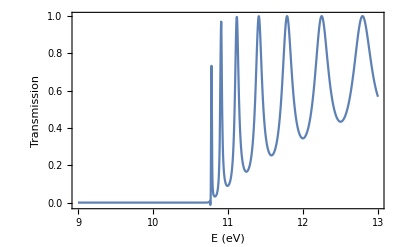

```mathematica
plot2=Plot[f[x],{x,9,13}, Frame->True, FrameLabel-> {"E (eV)","Transmission"}]
```

```mathematica
(*ATTENTION!!!! 
It seems there is an intstability in the stepped method when the barrier first appears*)
```

```mathematica
(*Comparison between transmission coefficients - they match*)
```

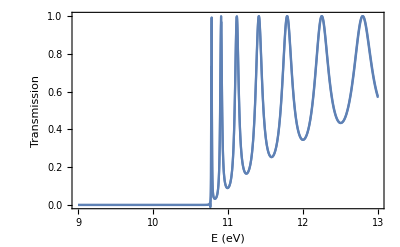

```mathematica
Show[plot1,plot2]
```